```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/368nm.dat"]
```

{{1.46129,-0.973787},{1.36603,-0.854584},{1.32759,-0.828074},{1.2815,-0.798485},{1.23231,-0.794981},{1.21009,-0.753959},{1.18279,-0.823347},{1.15809,-1.02471},{1.13892,-1.22827},{1.12738,-1.37626},{1.09219,-1.13451},{1.09146,-0.895974},{1.09503,-0.649035},{1.10053,-0.625713},{1.1079,-0.616297},{1.12128,-0.612323},{1.13179,-0.683751},{1.14273,-0.642872},{1.16583,-0.659461},{1.1846,-0.654715},{1.20387,-0.65616},{1.22314,-0.691209},{1.24682,-0.686827}}

-0.717212-0.0791959 x

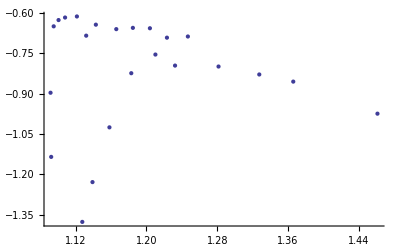

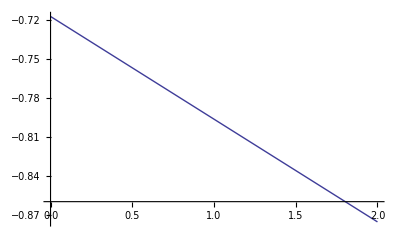

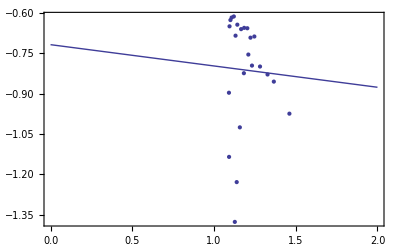

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```